```mathematica
caax={First[Values[(#MatrixData&/@Select[$LifeData,#Class==="Gun"&&#Period==15&]//Quiet)]],0};
```

### CAHistory

Removed ugly decay argument fixed colors

```mathematica
ClearAll@CellularAutomatonHistoryPlot
Options[CellularAutomatonHistoryPlot] = {Mesh->True, MeshStyle->Opacity[.1],ColorRules->{-1->Black, x_:>Blend[Lighter[{RGBColor[1., 1., 1.],RGBColor[0.98, 0.8623999999999999, 0.6859999999999999],RGBColor[1., 0.5267999999999999, 0.08999999999999997],RGBColor[0.89, 0.274476, 0.08009999999999998]}, .2],x]}, "Decay"-> .8};
CellularAutomatonHistoryPlot[rule_,init_,t_,opts___]:=
Module[{allops = Merge[{Options[CellularAutomatonHistoryPlot],opts},Last]},
ArrayPlot[
With[{u=
ArrayPad[#, 1]&/@CellularAutomaton[rule,init,t]},MapThread[If[#2==1,-1,#]&,{Fold[allops["Decay"] #+#2&,u],Last[u]},2]],Sequence@@FilterRules[Normal@allops, Options[ArrayPlot]]]]
```

Added padding, I think reducing meshstyle makes colors pop nicely:

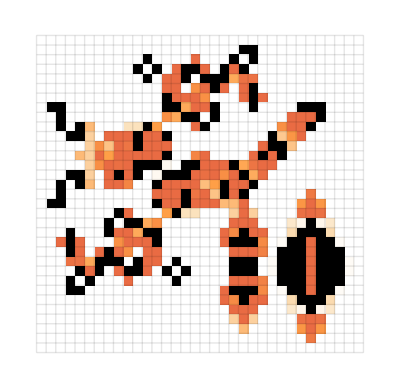

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",caax,44,"Decay"-> .8]
```

### Vids

Old:

```mathematica
ClearAll@CellularAutomatonHistoryPlot3DInteractive
CellularAutomatonHistoryPlot3DInteractive[rule_,init_,t_,opts___]:=
ListAnimate[Table[(ArrayPlot3D[
CellularAutomaton[rule,init,t],
  ColorFunction->(If[#==1,SetAlphaChannel[ RGBColor[1., 0.6436, 0.03622, 1.],1],Transparent] &),
  ColorFunctionScaling->False,ImageSize->500,Mesh->True,MeshStyle->Opacity[.3],ClipPlanes->{{0,0,-1,tt}},opts
]),{tt,1,t,1}]]
```

Downward version

```mathematica
ClearAll@CellularAutomatonHistoryPlot3DInteractive
CellularAutomatonHistoryPlot3DInteractive[rule_,init_,t_,opts___]:=
ListAnimate[Table[(ArrayPlot3D[
MapAt[#/. 1-> 2&, CellularAutomaton[rule,init,tt], -1],
  ColorFunction->(If[#==1,SetAlphaChannel[RGBColor[1., 0.6436, 0.03622, 1.],1],If[# == 2, SetAlphaChannel[(*RGBColor[1., 0.4, 0.03622]*)RGBColor[1., 0.6436, 0.03622, 1.],1], Transparent]] &),
  ColorFunctionScaling->False,ImageSize->500,Mesh->True,MeshStyle->Opacity[.3],opts
]),{tt,0, t,1}]]
```

From the side

#2

#2

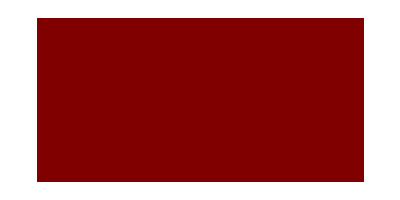

```mathematica
ArrayPlot[{{1, 1}}, ColorFunctionScaling->False, ColorFunction-> (If[Echo[#2] ==1, Blue, White]&)]
```

```mathematica
ClearAll@CellularAutomatonHistoryPlot3DInteractive
CellularAutomatonHistoryPlot3DInteractive[rule_,init_,t_,opts___]:=
ListAnimate[Table[(ArrayPlot3D[
Transpose[CellularAutomaton[rule,init,tt]],
  ColorFunction->(If[#==1,SetAlphaChannel[ RGBColor[1., 0.6436, 0.03622, 1.],1],If[# == 2, SetAlphaChannel[ RGBColor[1., 0.32, 0.03622],1], Transparent]] &),
  ColorFunctionScaling->False,ImageSize->500,Mesh->True,MeshStyle->Opacity[.3],opts]),{tt,0, t,1}]]
```

```mathematica
CellularAutomatonHistoryPlot3DInteractive["GameOfLife",caax,10,Mesh->True,MeshStyle->Opacity[.1]]
```

Upward

```mathematica
CellularAutomatonHistoryPlot3DInteractive["GameOfLife",caax,10,Mesh->True,MeshStyle->Opacity[.1]]
```

```mathematica
ArrayPlot3D[
CellularAutomaton["GameOfLife",caax,8],
  ColorFunction->(If[#==1,SetAlphaChannel[ RGBColor[1., 0.6436, 0.03622, 1.],1],Transparent] &),
  ColorFunctionScaling->False,ImageSize->500,Mesh->True,MeshStyle->Opacity[.3], ViewPoint->{2, -2, -1.5}, Lighting->"Accent"]
```

-Graphics3D-

Downward

```mathematica
CellularAutomatonHistoryPlot3DInteractive["GameOfLife",caax,20,Mesh->True,MeshStyle->Opacity[.1], ViewPoint->{2, -2, -1.5}, Boxed->True]
```

```mathematica
KeyExistsQ[Association[Options[ArrayPlot3D]], Lighting]
```

True

```mathematica
l1=AmbientLight[GrayLevel[.3]];
l2=DirectionalLight[Orange,{{1,1,1},{0,0,0}}];
```

```mathematica
CellularAutomatonHistoryPlot3DInteractive["GameOfLife",caax,20,Mesh->True,MeshStyle->Opacity[.1], ViewPoint->{2, -2, -1.5},  Lighting->DirectionalLight[White,{{5,5,-10},{-5 ,-5, 10}}], Boxed->False]
```

### CASpacetime

```mathematica
ClearAll@CellularAutomatonSpacetimePlot
CellularAutomatonSpacetimePlot[rule_,init_,t_,opts___]:=
Module[{allops = Merge[{Options[CellularAutomatonHistoryPlot],opts},Last]},
ArrayPlot[With[{u=Transpose@CellularAutomaton[rule,init,t]},
MapThread[If[#2==1,-1,#]&,{Fold[allops["Decay"] #+#2&,u],Last[u]},2]],Sequence@@FilterRules[Normal@allops, Options[ArrayPlot]]]]
```

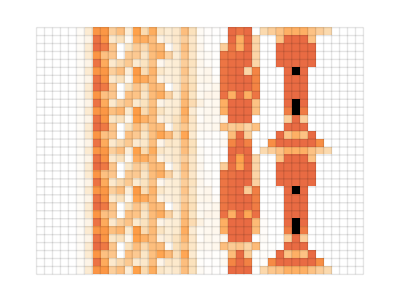

```mathematica
CellularAutomatonSpacetimePlot["GameOfLife",caax,{30, Automatic, {-5, 35}},"Decay"->.8]
```

```mathematica
caax
```

{SparseArray[…],0}

```mathematica
CellularAutomatonSpacetimePlot["GameOfLife",caax,{30, Automatic, {-5, 35}},"Decay"->.8]
```

-Graphics-

### Boxed layered graph, as well as showing matrices as nodes

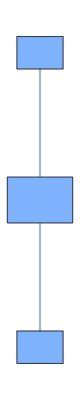
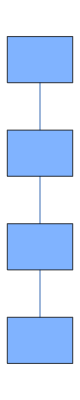
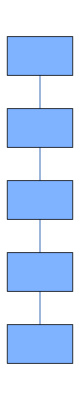
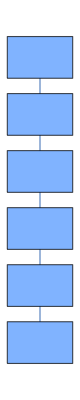
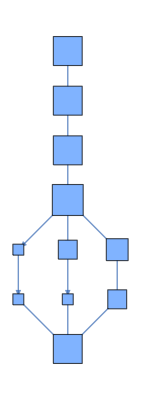
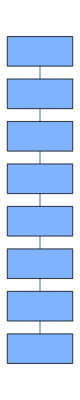
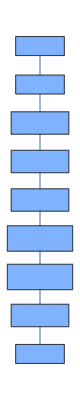
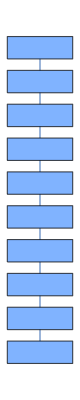

```mathematica
LayeredGraph[LifeMultiwayGraph[LifeClosure[#["MatrixData"]]],VertexSize->{x_:>(.25Sqrt[Times@@{Max[#[[2, 1]]  -  #[[2, 1]] ,1],Max[#[[2, 2]] - #[[2, 1]], 1]}&@CoordinateBounds[Last[x]]])}, VertexShapeFunction->"Square"]&/@ Take[allosc, 30]
```